```mathematica
x=1
l=2
x*l
x+l
```

1

2

2

3

The brackets have a a different uses, from defining functions to making lists. 3 types are used: (),{}, []. They’re used for grouping in formulae, denote a sequence, and function arguments, respectively. For functions the convention in Mathematica is to use CamelCase.

```mathematica
3(l*2-x)^2
```

27

```mathematica
list4 = {x-1,x,x+1}
```

{0,1,2}

```mathematica
list4^2
```

{0,1,4}

```mathematica
1/list4
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,1,1/2}

```mathematica
N[π,10]
```

```mathematica
3.14159265358979323845859885078191098273`10.
```

```mathematica
?N
```

```mathematica
Sqrt[2]
Sin[π/3]
```

√2

(√3)/2

There are some functions that can be used to simplify expressions, like Expand

```mathematica
Expand[(a+b)^2]
```

a^2+2 a b+b^2

```mathematica
Expand[(a+b)^4]
```

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4

```mathematica
Collect[Expand[(a+b)^4],a]
```

```mathematica
a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4
```

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4

As with any good Notebook application, we can create plots in a simple and convenient way



```mathematica
Plot[Sin[x], {x,0,2π}]
```

```mathematica
?Plot
```

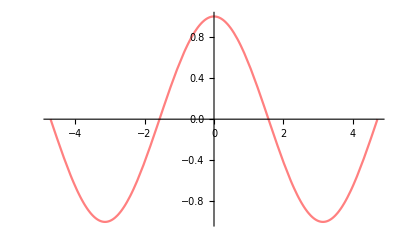

```mathematica
Plot[Cos[x],{x,-3π/2,3π/2}, PlotStyle->Pink]
```

Obviously we can also do the classic 3d plot.

```mathematica
Plot3D[Sin[x]Cos[y], {x,-2π,2π}, {y,-2π, 2π}, Mesh->None]
Plot3D[Sin[x]Tan[y], {x,-2π,2π}, {y,-2π, 2π}, Mesh->None]
Plot3D[Cos[y x], {x,-2π,2π}, {y,-2π, 2π}, Mesh->None]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

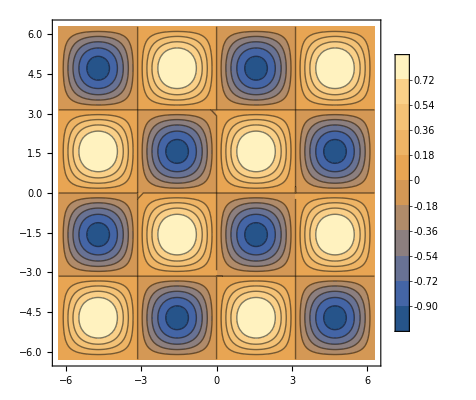

```mathematica
ContourPlot[Sin[x]Sin[y], {x,-2π,2π}, {y,-2π,2π}, Contours->10, PlotLegends->Automatic]
```

```mathematica
sinValues = Table[ Sin[2π k/24] +RandomReal[{-.3,.3}], {k,1,28}]
```

{0.0545524,0.529319,0.974391,0.658373,0.746168,0.908321,0.721223,0.889903,0.901184,0.20611,0.481607,-0.0204629,0.00282087,-0.251548,-0.501706,-0.65794,-1.21235,-0.701821,-0.77118,-1.04943,-0.828115,-0.753484,-0.502355,0.100189,0.0142883,0.435578,0.915302,1.10405}

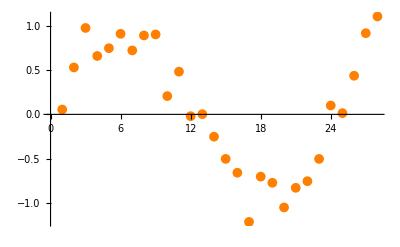

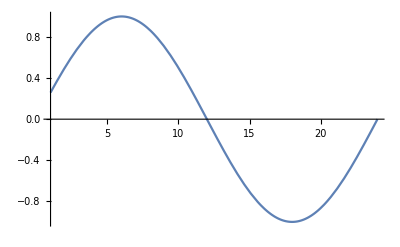

```mathematica
lpx = ListPlot[sinValues, PlotMarkers->{Automatic, Medium}, PlotStyle->Orange]
cpx = Plot[Sin[2π x/24], {x,1,24}]
```

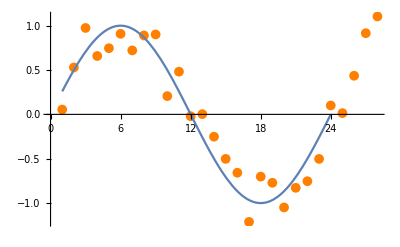

```mathematica
Show[lpx,cpx]
```

It would be hard to program without functions. Procedural programming can be fun but does not scale well. We need functions

```mathematica
f[x_] := 1/Sqrt[x]
```

```mathematica
{f[2], f[0],f[9]}
```

Power::infy: Infinite expression 1/0 encountered.

{1/(√2),ComplexInfinity,1/3}

```mathematica
g[x_Real,n_Int]:=(1+x)/n
hump[x_,xmax_]:=(x-xmax)^2/xmax
```

```mathematica
g[2,2] (*{g[π,2],g[π,4],g[π,5]}*)
hump[1,2]
```

3/2

1/2

```mathematica
fac[n_ /; n<0]:= "NaN"
fac[0]:=1
fac[n_/; n>0]:= n fac[n-1]
```

```mathematica
fac[3]
```

6

And here' s where the fun of Mathematica starts. We can do automatic differentiation and integration, in a straightforward way!

```mathematica
{D[Log[x],x], D[f[x],x]}
```

{1/x,-1/(2 x^(3/2))}

```mathematica
{Integrate[Log[x],x],Integrate[f[x],x]}
```

{-x+x Log[x],2 √x}

Like any other scientific computing suite, we can also do linear algebra

```mathematica
M = {{1,2},{3,4}}
A = {{9,3},{4,6}}
MatrixForm[M]
Inverse[M]
```

{{1,2},{3,4}}

{{9,3},{4,6}}

(1 | 2
3 | 4)

{{-2,1},{3/2,-1/2}}

```mathematica
MA = M.A
MAinv=M.Inverse[A]
MatrixForm[MA]
MatrixForm[MAinv]
Eigenvectors[MAinv]
Eigenvalues[MAinv]
```

{{17,15},{43,33}}

{{-1/21,5/14},{1/21,9/14}}

(17 | 15
43 | 33)

(-1/21 | 5/14
1/21 | 9/14)

{{1/2,1},{-15,1}}

{2/3,-1/14}

```mathematica
J = {{0,-1},{1,0}}
Eigenvalues[J]
Eigenvectors[J]
```

{{0,-1},{1,0}}

{ⅈ,-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

We can even solve equations!

```mathematica
Solve[x^I+4==3,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-1)^-ⅈ}}

Furthermore we can even find numerical solutions to differential equations

```mathematica
Clear[Derivative] (* When I started instead of using == below I used =, and Derivative took a value, so we need to clear it*)
LorenzAttractor={
  x'[t]==σ*(y[t]-x[t]),
  y'[t]==x[t] (ρ -z[t]) - y[t],
  z'[t]==x[t] y[t]-β z[t]
} /.{σ->9, β->9/4, ρ->28}
IVP = {x[0]==.1, y[0]==.1,z[0]==.1}
```

{x'[t]==9 (-x[t]+y[t]),y'[t]==-y[t]+x[t] (28-z[t]),z'[t]==x[t] y[t]-(9 z[t])/4}

{x[0]==0.1,y[0]==0.1,z[0]==0.1}

```mathematica
LAns=NDSolve[Join[LorenzAttractor, IVP], {x,y,z}, {t,0,500}, MaxSteps->∞]
```

{{x→InterpolatingFunction[{{0., 500.}}, <>],y→InterpolatingFunction[{{0., 500.}}, <>],z→InterpolatingFunction[{{0., 500.}}, <>]}}

```mathematica
{X, Y, Z} = First[{x, y, z} /. LAns](*It's a list inside a list of one element *)
ParametricPlot3D[{X[t], Y[t], Z[t]}, {t, 0, 500}, PlotPoints -> 200, Boxed -> True, Axes -> True, PlotStyle -> Thin]
```

{InterpolatingFunction[{{0., 500.}}, <>],InterpolatingFunction[{{0., 500.}}, <>],InterpolatingFunction[{{0., 500.}}, <>]}

-Graphics3D-

```mathematica
Manipulate[ParametricPlot3D[{X[t],Y[t],Z[t]}, {t,0,T}, PlotPoints->200,Boxed->True,Axes->False, PlotStyle->Thin, PlotRange->{{-30,30},{-30,30},{0,60}}], {T,0.1,500,1}]
```

We can also, of course, add whatever text we want, labels, titles, to plots, useful for exporting and using in another latex file.

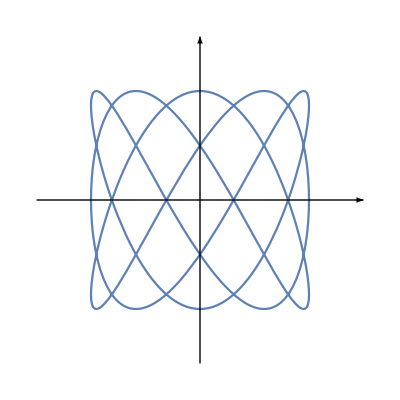

```mathematica
p = ParametricPlot[{Cos[3t],Sin[5t]}, {t,0,2π}, Axes-> None];
ax= Graphics[{Arrowheads[0.05], Arrow[{{-1.5,0},{1.5,0}}]}];
ay= Graphics[{Arrowheads[0.05], Arrow[{{0,-1.5},{0,1.5}}]}];
Show[p,ax,ay, PlotRange-> {{-1.5,1.5},{-1.5,1.5}}]
```

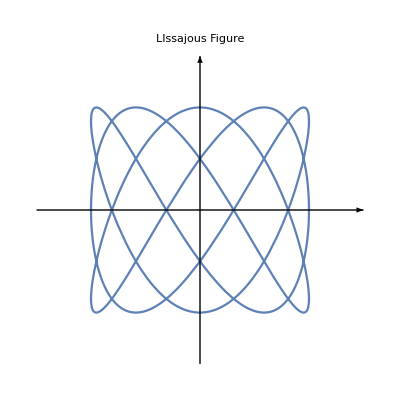

```mathematica
Show[%55,PlotLabel->HoldForm[LIssajous Figure],LabelStyle->{18,GrayLevel[0]}]
```

Since the first lab is just basic exercises and is not needed to hand in, I’ll just put some random stuff below that I’m not initially sure I’m able to figure out quickly.

```mathematica
Table[i,{i,-3,17}]
```

{-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

```mathematica
?Prime
?Select
```

```mathematica
Table[Prime[i], {i,1,100}] (*First 100 prime numbers*)
Select[Table[Prime[i], {i,1,100}], #<100&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
sep=2/100;
list1 = Table[i*sep,{i,-1/sep,1/sep}]
```

{-1,-49/50,-24/25,-47/50,-23/25,-9/10,-22/25,-43/50,-21/25,-41/50,-4/5,-39/50,-19/25,-37/50,-18/25,-7/10,-17/25,-33/50,-16/25,-31/50,-3/5,-29/50,-14/25,-27/50,-13/25,-1/2,-12/25,-23/50,-11/25,-21/50,-2/5,-19/50,-9/25,-17/50,-8/25,-3/10,-7/25,-13/50,-6/25,-11/50,-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5,11/50,6/25,13/50,7/25,3/10,8/25,17/50,9/25,19/50,2/5,21/50,11/25,23/50,12/25,1/2,13/25,27/50,14/25,29/50,3/5,31/50,16/25,33/50,17/25,7/10,18/25,37/50,19/25,39/50,4/5,41/50,21/25,43/50,22/25,9/10,23/25,47/50,24/25,49/50,1}

```mathematica
b=False;
For[i=1,i<=100,i++, 
  diff = Part[list1,i+1]-Part[list1,i];
  b = If[diff!=1/50, True, False];
  If[b==True, 
    Print["Not what we expected"];
    Break[], True]
 ]
If[b,Print["There was a different seperation!"], Print["Everything as expected"]]
```

Everything as expected

We can also do expansion of a function just with the function Series[func, {var, x_o, degree expansion}]

```mathematica
Series[Cos[x], {x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
Series[Cos[x], {x,π/2,8}] (*We can also choose any other x_0*)
```

-(x-π/2)+1/6 (x-π/2)^3-1/120 (x-π/2)^5+(x-π/2)^7/5040+O[x-π/2]^9

```mathematica
(*Clear[mcLaurinl, x,y,Cos,Series,Normal]*)
mcLaurinl[x_, n_Integer]:=Module[{y}, Normal[Series[Cos[y],{y,0,n}]]/.y->x]
```

```mathematica
For[i=0,i<=5, i++,
  Print[mcLaurinl[xxxx, i]]
]
```

1

1

1-xxxx^2/2

1-xxxx^2/2

1-xxxx^2/2+xxxx^4/24

1-xxxx^2/2+xxxx^4/24

```mathematica
p1=Plot[Cos[y], {y,-π,π}, PlotLabels->"Original"];
t1=Table[Plot[mcLaurin[s,i],{s,-π,π}, PlotStyle->i, PlotLabels->StringForm["MacLaurin ``.",i]], {i,4,7}];

Show[p1,t1, PlotRange->{{-8,8},{-1.5,1.5}}, PlotLegends->Automatic]
```

-Graphics-

```mathematica
F[t_Inte]:= mcLaurin[s,t]
```

```mathematica
Manipulate[Plot[mcLaurin[s,a],{s,-2π,2π}], {a,1,20,1}]
```

We can of course also solve equations

```mathematica
Solve[z^2-z+3==0]
```

```mathematica
{{z->1/2 (1-ⅈ √11)},{z->1/2 (1+ⅈ √11)}}
```

We ought to find the solution to the following system
-Graphics-

```mathematica
A = MatrixForm[{{1,2,-1,-4},{1,-1,2,0},{-3,-2,1,1},{0,0,0,0}}];
b =MatrixForm[{0,1,-1}];
v = {x,y,z,u};
eqs={
  x+2y-z-u==0,
  x-y+2z==1,
-3x-2y+z+u==-1
};
Solve[eqs,{x,y,z,u}];
cs= CoefficientArrays[eqs, Variables@eqs];
A=MatrixForm[cs[[2]]];
Aaug = Transpose[Join[Transpose[A],{b}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Join::heads: Heads Transpose and List at positions 1 and 2 are expected to be the same.

Transpose[Join[Transpose[(-1 | 1 | 2 | -1
0 | 1 | -1 | 2
1 | -3 | -2 | 1)],{(0
1
-1)}]]

```mathematica
Aaug
```

```mathematica
Transpose[Join[Transpose[({{-1, 1, 2, -1}, {0, 1, -1, 2}, {1, -3, -2, 1}})],{({{0}, {1}, {-1}})}]]
```

Well we just had an experience that leave as evident the inferiority of Mathematica as a text editor. Doing a wrong sequence of keystrokes I lost my exercise 6(a), cos the notebook somehow got deleted and Ctrl-Z did not work. So I’m not doing it again, and instead going directly into the Van der Pol oscillator 6(b).

```mathematica
VdP={
  x'[t]==y[t],
  y'[t]==(1-x[t]^2)y[t]-x[t]
};
VdPIVP={
  x[0]==1,
  y[0]==1
};
VdPSol =NDSolve[Join[VdP,VdPIVP], {x,y},{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
{X,Y}=First[{x,y}/.VdPSol]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

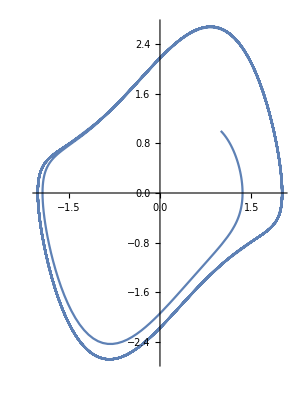

```mathematica
ParametricPlot[{X[t],Y[t]},{t,0,100}]
```

```mathematica
Manipulate[
  VdPSol=NDSolve[Join[VdP,{x[0]==icx,y[0]==icy}], {x,y},{t,0,100}];
  {X,Y}=First[{x,y}/.VdPSol];
  ParametricPlot[{X[t],Y[t]},{t,0,100}]
, {icx,-10,10},{icy,-10,10}]
Locator
```

NDSolve::deqn: Equation or list of equations expected instead of Join[VdP,{x[0]==2.45,y[0]==4.55}] in the first argument Join[VdP,{x[0]==2.45,y[0]==4.55}].

ReplaceAll::reps: {NDSolve[Join[VdP,{x[0]==2.45,y[0]==4.55}],{x,y},{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.